# Fermi nuclear potential

## This notebook calculates the Fermi nuclear potential using the series expansions given in Johnson AST(2007).

Introduce parameters of the nucleus:

```mathematica
(*
Z=83;
Rr=5.521;
Bohrradius=5.29177210920000000000 10^-11;
a=(.523387555*10^-15/Bohrradius);
t=4 Log[3] a Bohrradius;
c=(Sqrt[(5/3)*Rr^2-(7/3)(0.52338755*Pi)^2]*10^-15/Bohrradius) 
rms=(Rr*10^-15/Bohrradius)
*)
Z=1;
c=1;
a=1/4;
Num=100;
```

```mathematica
S[k_]:=∑_(n=1)^Num (-1)^(n-1)/n^k Exp[-n c/a];
P[k_,r_]:=∑_(n=1)^Num (-1)^(n-1)/n^k Exp[-n Abs[r-c]/a];
```

```mathematica
A=1+(π^2 a^2)/c^2+(6 a^3)/c^3 S[3];
B=1+(10 π^2 a^2)/(3 c^2)+(7 π^4 a^4)/(3 c^4)+(120 a^5)/c^5 S[5];
```

Test the Rrms consistency:

```mathematica
(*Rrms=c √(3/5 (B/A))*)
```

```mathematica
(*Δrms = Abs[Rrms-rms]*)
```

Define Fermi potential:

```mathematica
VF[r_]:=Piecewise[{{Z/(A c)(3/2-r^2/(2 c^2)+(π^2 a^2)/(2 c^2)+(3 a^2)/c^2 P[2,r] +(6 a^3)/(c^2 r) (S[3]-P[3,r])),r≤c},{Z/(A r)(1+(π^2 a^2)/c^2+(6 a^3)/(c^2 r) (S[3]-P[3,r])-(3 r a^2)/c^3 P[2,r]),r>c}}];
```

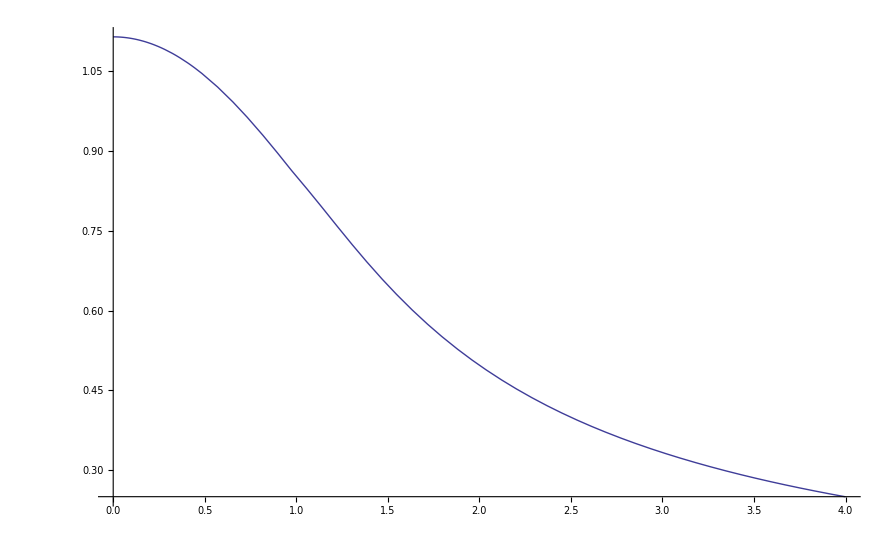

```mathematica
Plot[VF[r],{r,0,4},Exclusions->None]
```

Define hard-sphere potential:

```mathematica
VHS[x_]:= Piecewise[{{((Z/c) (3/2-x^2/(2 c^2))),x≤c},{(Z/x),x>c}}];
```

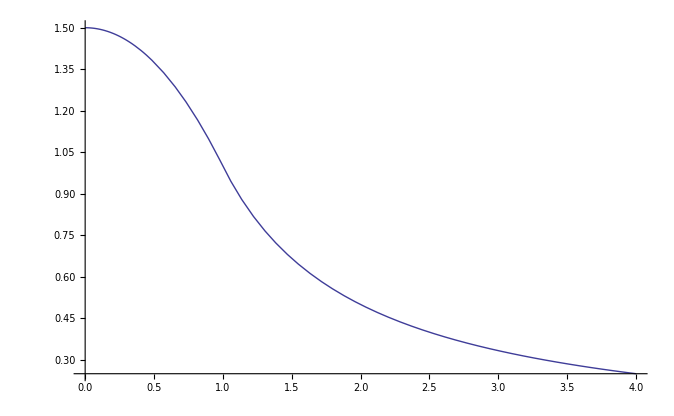

```mathematica
Plot[VHS[r],{r,0,4},Exclusions->None]
```

Define Coulomb potential:

```mathematica
V[x_]:= Z/x;
```

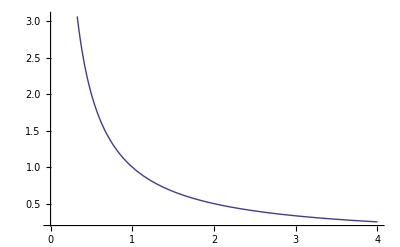

```mathematica
Plot[V[r],{r,0,4},Exclusions->None]
```

Compare Hard-Sphere and Fermi Potential:

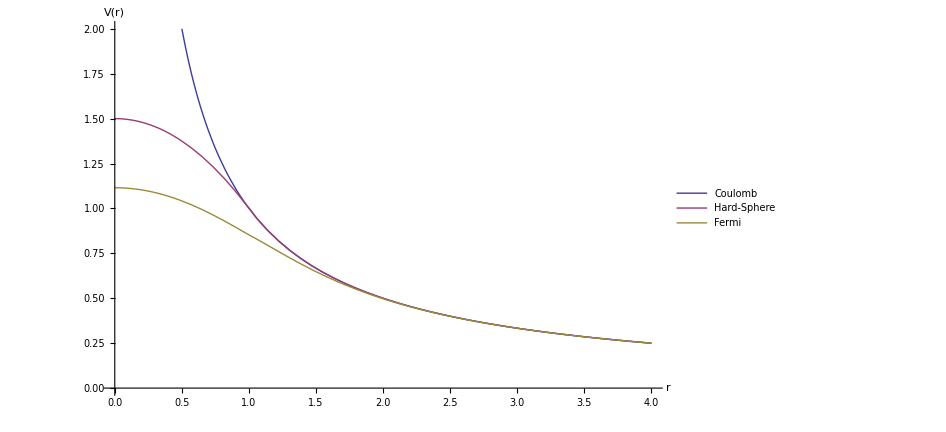

```mathematica
Plot[{V[r],VHS[r],VF[r]},{r,0,4},PlotRange->{{0,4},{0,2}},Exclusions->None,PlotLegends->{"Coulomb","Hard-Sphere", "Fermi"},AxesLabel->{"r","V(r)"},LabelStyle->{"Medium"}]
```